```mathematica
A=({{1/6, -1/2, -1/2}, {-1/2, 1/6, 1/2}, {1, -1, -4/3}})
```

{{1/6,-1/2,-1/2},{-1/2,1/6,1/2},{1,-1,-4/3}}

Mi calcolo gli autovalori di A

```mathematica
λ=Eigenvalues[A]
```

{-1/3,-1/3,-1/3}

Ricordiamoci che i modi naturali del sistema si ottengono valutando la molteplicita’ algebrica del POLINOMIO MINIMO per ciascun autovalore

```mathematica
Simplify[ResourceFunction["MatrixMinimalPolynomial"][A,x]]
```

1/9 (1+3 x)^2

Grafico del modo polinomial-potenza di primo grado

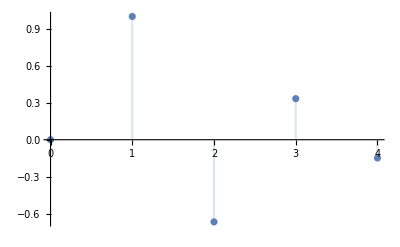

```mathematica
DiscretePlot[k (-1/3)^(k-1),{k,0,4},PlotRange->All]
```

Vediamo la forma di Jordan di A

```mathematica
JordanDecomposition[A][[2]]//MatrixForm
```

(-1/3 | 0 | 0
0 | -1/3 | 1
0 | 0 | -1/3)

```mathematica
Subscript[A, J]=JordanDecomposition[A][[2]]
```

{{-1/3,0,0},{0,-1/3,1},{0,0,-1/3}}

```mathematica
MatrixPower[Subscript[A, J],k]//MatrixForm
```

((-1/3)^k | 0 | 0
0 | (-1/3)^k | -(-1)^k 3^(1-k) k
0 | 0 | (-1/3)^k)

A